## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PPS";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef_1/";*)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy.csv";

mainFolder = "fit_PPS_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:C:\MASSef\examples\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(atp^c+h2o^c+pyr^c⇌amp^c+2 h^c+pep^c+pi^c)^PPS

;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
pyr | Null | 2.41 | 2.2895
2.5305 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | 0.000028 | 0.0000266
0.0000294 |  | M | 7.5 | 25 |  | 
1 | pyr | 0.000083 | 0.00007885
0.00008715 |  | M | 7.5 | 25 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
pyr | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  | 
1 | pep | Null
pi | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(atp^c+h2o^c+pyr^c⇌amp^c+2 h^c+pep^c+pi^c)^PPS

;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
pyr | Null | 2.41 | 2.2895
2.5305 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | 0.000028 | 0.0000266
0.0000294 |  | M | 7.5 | 25 |  | 
1 | pyr | 0.000083 | 0.00007885
0.00008715 |  | M | 7.5 | 25 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
pyr | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  | 
1 | pep | Null
pi | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
Overscript[atp^c+h2o^c+pyr^c⇌amp^c+2 h^c+pep^c+pi^c, PPS]
```

```mathematica
catalyticBranch={"E_PPS[c] + pyr[c] <=> E_PPS[c]&pyr",
				"E_PPS[c]&pyr + atp[c] <=> E_PPS[c]&pyr&atp",

				"E_PPS[c]&pyr&atp <=> E_PPS[c]&pep&amp&pi",
				
				"E_PPS[c]&pep&amp&pi <=> E_PPS[c]&pep&amp + pi[c]",
				"E_PPS[c]&pep&amp <=> E_PPS[c]&pep + amp[c]",
				"E_PPS[c]&pep <=> E_PPS[c] + pep[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PPS^c)_^+pyr^c⇌(PPS^c&pyr^c)_^)^PPS1,((PPS^c&pep^c)_^⇌(PPS^c)_^+pep^c)^PPS2,((PPS^c&pyr^c)_^+atp^c⇌(PPS^c&pyr^c&atp^c)_^)^PPS3,((PPS^c&pep^c&amp^c)_^⇌(PPS^c&pep^c)_^+amp^c)^PPS4,((PPS^c&pyr^c&atp^c)_^⇌(PPS^c&pep^c&amp^c&pi^c)_^)^PPS5,((PPS^c&pep^c&amp^c&pi^c)_^⇌(PPS^c&pep^c&amp^c)_^+pi^c)^PPS6}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PPS^c)_^+pyr^c⇌(PPS^c&pyr^c)_^)^PPS1,Overscript[(PPS^c&pep^c)_^⇌(PPS^c)_^+pep^c, PPS2],((PPS^c&pyr^c)_^+atp^c⇌(PPS^c&pyr^c&atp^c)_^)^PPS3,Overscript[(PPS^c&pep^c&amp^c)_^⇌(PPS^c&pep^c)_^+amp^c, PPS4],((PPS^c&pyr^c&atp^c)_^⇌(PPS^c&pep^c&amp^c&pi^c)_^)^PPS5,Overscript[(PPS^c&pep^c&amp^c&pi^c)_^⇌(PPS^c&pep^c&amp^c)_^+pi^c, PPS6]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PPS^c&pyr^c&atp^c)_^-((PPS^c&pep^c&amp^c&pi^c)_^)/K_PPS5) Volume_c k_PPS5^⟶}

Volume_c (-(PPS^c&pep^c&amp^c&pi^c)_^ k_PPS5^⟵+(PPS^c&pyr^c&atp^c)_^ k_PPS5^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	amp[c]	atp[c]	pep[c]	pi[c]	pyr[c]	param_PPS_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\haldaneRatio_1.txt"	2.41
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\haldaneRatio_1.txt"	2.41
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\haldaneRatio_1.txt"	2.41
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\haldaneRatio_1.txt"	2.41
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\haldaneRatio_1.txt"	2.41
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\haldaneRatio_1.txt"	2.41
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\haldaneRatio_1.txt"	2.41
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\haldaneRatio_1.txt"	2.41
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\haldaneRatio_1.txt"	2.41
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\haldaneRatio_1.txt"	2.41
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\haldaneRatio_1.txt"	2.41
1	0	2.800000000000001e-6	0	0	1	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_atp.txt"	0.09090909090909094
1	0	4.4377009388911215e-6	0	0	1	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_atp.txt"	0.1368068886032101
1	0	7.033282008226834e-6	0	0	1	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_atp.txt"	0.20076000891310197
1	0	0.00001114700077549792	0	0	1	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_atp.txt"	0.28474724895080133
1	0	0.000017666805645445413	0	0	1	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_atp.txt"	0.38686317984685703
1	0	0.000028000000000000013	0	0	1	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_atp.txt"	0.5000000000000001
1	0	0.00004437700938891122	0	0	1	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_atp.txt"	0.6131368201531433
1	0	0.00007033282008226833	0	0	1	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_atp.txt"	0.7152527510491988
1	0	0.0001114700077549793	0	0	1	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_atp.txt"	0.7992399910868985
1	0	0.00017666805645445412	0	0	1	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_atp.txt"	0.86319311139679
1	0	0.00028000000000000014	0	0	1	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_atp.txt"	0.9090909090909092
1	0	1	0	0	8.299999999999997e-6	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_pyr.txt"	0.09090909090909087
1	0	1	0	0	0.000013154613497427242	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_pyr.txt"	0.13680688860321
1	0	1	0	0	0.000020848657381529523	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_pyr.txt"	0.2007600089131018
1	0	1	0	0	0.00003304289515594023	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_pyr.txt"	0.2847472489508011
1	0	1	0	0	0.000052369459591856	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_pyr.txt"	0.3868631798468568
1	0	1	0	0	0.00008299999999999997	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_pyr.txt"	0.4999999999999999
1	0	1	0	0	0.00013154613497427242	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_pyr.txt"	0.6131368201531431
1	0	1	0	0	0.00020848657381529524	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_pyr.txt"	0.7152527510491987
1	0	1	0	0	0.0003304289515594027	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_pyr.txt"	0.7992399910868982
1	0	1	0	0	0.0005236945959185599	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_pyr.txt"	0.86319311139679
1	0	1	0	0	0.0008299999999999997	1			"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\relRateFor_pyr.txt"	0.9090909090909091
1	0	1	0	0	1	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateFor.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"C:\MASSef\examples\fit_PPS_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

FilePrint::badfile: The specified argument psoParameterPath should be a valid string or File.

FilePrint[psoParameterPath]

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	18
filesWithFunctions	[C:\\MASSef\\examples\\fit_PGK_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\relRateFor_13dpg.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\relRateFor_adp.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\relRateRev_3pg.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\relRateRev_atp.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\haldaneRatio_2.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\haldaneRatio_3.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\haldaneRatio_4.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.0493349212650283
best_fit: 0.7364190272692174
best_fit: 2.950147180378698
best_fit: 1.0903897522518224
best_fit: 2.950314629467755
best_fit: 1.088744497081865
best_fit: 0.8096309128424378
best_fit: 0.6529575193245898
best_fit: 1.0130370977288465
best_fit: 0.8578137048494765

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 2.907×10^-11 | 8.45063×10^-22 | 1.61316×10^-10 | 6.6936×10^-9 | 2.41 | 2.41
1 | haldaneRatio_1 | 2.907×10^-11 | 8.45063×10^-22 | 1.61316×10^-10 | 6.6936×10^-9 | 2.41 | 2.41
1 | haldaneRatio_1 | 2.907×10^-11 | 8.45063×10^-22 | 1.61316×10^-10 | 6.6936×10^-9 | 2.41 | 2.41
1 | haldaneRatio_1 | 2.907×10^-11 | 8.45063×10^-22 | 1.61316×10^-10 | 6.6936×10^-9 | 2.41 | 2.41
1 | haldaneRatio_1 | 2.907×10^-11 | 8.45063×10^-22 | 1.61316×10^-10 | 6.6936×10^-9 | 2.41 | 2.41
1 | haldaneRatio_1 | 2.907×10^-11 | 8.45063×10^-22 | 1.61316×10^-10 | 6.6936×10^-9 | 2.41 | 2.41
1 | haldaneRatio_1 | 2.907×10^-11 | 8.45063×10^-22 | 1.61316×10^-10 | 6.6936×10^-9 | 2.41 | 2.41
1 | haldaneRatio_1 | 2.907×10^-11 | 8.45063×10^-22 | 1.61316×10^-10 | 6.6936×10^-9 | 2.41 | 2.41
1 | haldaneRatio_1 | 2.907×10^-11 | 8.45063×10^-22 | 1.61316×10^-10 | 6.6936×10^-9 | 2.41 | 2.41
1 | haldaneRatio_1 | 2.907×10^-11 | 8.45063×10^-22 | 1.61316×10^-10 | 6.6936×10^-9 | 2.41 | 2.41
1 | haldaneRatio_1 | 2.907×10^-11 | 8.45063×10^-22 | 1.61316×10^-10 | 6.6936×10^-9 | 2.41 | 2.41
1 | relRateFor_atp | 4.51544×10^-6 | 2.03892×10^-11 | 9.45194×10^-7 | 0.00103971 | 0.0909091 | 0.0909081
1 | relRateFor_atp | 3.67352×10^-6 | 1.34948×10^-11 | 1.15719×10^-6 | 0.000845857 | 0.136807 | 0.136806
1 | relRateFor_atp | 2.50041×10^-6 | 6.25206×10^-12 | 1.15585×10^-6 | 0.000575739 | 0.20076 | 0.200759
1 | relRateFor_atp | 9.59799×10^-7 | 9.21215×10^-13 | 6.29296×10^-7 | 0.000221002 | 0.284747 | 0.284747
1 | relRateFor_atp | 9.13361×10^-7 | 8.34229×10^-13 | 8.1361×10^-7 | 0.000210309 | 0.386863 | 0.386864
1 | relRateFor_atp | 2.98869×10^-6 | 8.93228×10^-12 | 3.44087×10^-6 | 0.000688174 | 0.5 | 0.500003
1 | relRateFor_atp | 5.06403×10^-6 | 2.56444×10^-11 | 7.14944×10^-6 | 0.00116604 | 0.613137 | 0.613144
1 | relRateFor_atp | 6.93722×10^-6 | 4.8125×10^-11 | 0.0000114252 | 0.00159737 | 0.715253 | 0.715264
1 | relRateFor_atp | 8.47787×10^-6 | 7.18742×10^-11 | 0.0000156021 | 0.00195212 | 0.79924 | 0.799256
1 | relRateFor_atp | 9.65101×10^-6 | 9.3142×10^-11 | 0.0000191823 | 0.00222225 | 0.863193 | 0.863212
1 | relRateFor_atp | 0.000010493 | 1.10102×10^-10 | 0.0000219647 | 0.00241612 | 0.909091 | 0.909113
1 | relRateFor_pyr | 0.0000133818 | 1.79072×10^-10 | 2.80111×10^-6 | 0.00308122 | 0.0909091 | 0.0909063
1 | relRateFor_pyr | 0.0000108862 | 1.1851×10^-10 | 3.42923×10^-6 | 0.00250662 | 0.136807 | 0.136803
1 | relRateFor_pyr | 7.409×10^-6 | 5.48933×10^-11 | 3.42491×10^-6 | 0.00170597 | 0.20076 | 0.200757
1 | relRateFor_pyr | 2.84242×10^-6 | 8.07936×10^-12 | 1.86364×10^-6 | 0.000654489 | 0.284747 | 0.284745
1 | relRateFor_pyr | 2.70992×10^-6 | 7.34367×10^-12 | 2.41397×10^-6 | 0.000623984 | 0.386863 | 0.386866
1 | relRateFor_pyr | 8.86158×10^-6 | 7.85277×10^-11 | 0.0000102024 | 0.00204048 | 0.5 | 0.50001
1 | relRateFor_pyr | 0.0000150133 | 2.254×10^-10 | 0.0000211962 | 0.00345701 | 0.613137 | 0.613158
1 | relRateFor_pyr | 0.0000205659 | 4.22956×10^-10 | 0.0000338714 | 0.00473559 | 0.715253 | 0.715287
1 | relRateFor_pyr | 0.0000251328 | 6.31657×10^-10 | 0.0000462536 | 0.0057872 | 0.79924 | 0.799286
1 | relRateFor_pyr | 0.0000286103 | 8.1855×10^-10 | 0.000056867 | 0.00658799 | 0.863193 | 0.86325
1 | relRateFor_pyr | 0.0000311061 | 9.67588×10^-10 | 0.0000651154 | 0.0071627 | 0.909091 | 0.909156
1 | absRateFor | 2.16448×10^-9 | 4.68499×10^-18 | 1.49657×10^-7 | 4.98391×10^-7 | 30.0281 | 30.0281
1 | absRateFor | 2.16448×10^-9 | 4.68499×10^-18 | 1.49657×10^-7 | 4.98391×10^-7 | 30.0281 | 30.0281
1 | absRateFor | 2.16448×10^-9 | 4.68499×10^-18 | 1.49657×10^-7 | 4.98391×10^-7 | 30.0281 | 30.0281
1 | absRateFor | 2.16448×10^-9 | 4.68499×10^-18 | 1.49657×10^-7 | 4.98391×10^-7 | 30.0281 | 30.0281
1 | absRateFor | 2.16448×10^-9 | 4.68499×10^-18 | 1.49657×10^-7 | 4.98391×10^-7 | 30.0281 | 30.0281
1 | absRateFor | 2.16448×10^-9 | 4.68499×10^-18 | 1.49657×10^-7 | 4.98391×10^-7 | 30.0281 | 30.0281
1 | absRateFor | 2.16448×10^-9 | 4.68499×10^-18 | 1.49657×10^-7 | 4.98391×10^-7 | 30.0281 | 30.0281
1 | absRateFor | 2.16448×10^-9 | 4.68499×10^-18 | 1.49657×10^-7 | 4.98391×10^-7 | 30.0281 | 30.0281
1 | absRateFor | 2.16448×10^-9 | 4.68499×10^-18 | 1.49657×10^-7 | 4.98391×10^-7 | 30.0281 | 30.0281
1 | absRateFor | 2.16448×10^-9 | 4.68499×10^-18 | 1.49657×10^-7 | 4.98391×10^-7 | 30.0281 | 30.0281
1 | absRateFor | 2.16448×10^-9 | 4.68499×10^-18 | 1.49657×10^-7 | 4.98391×10^-7 | 30.0281 | 30.0281
1 | absRateRev | 1.22439×10^-10 | 1.49914×10^-20 | 8.46572×10^-9 | 2.81927×10^-8 | 30.0281 | 30.0281
1 | absRateRev | 1.22439×10^-10 | 1.49914×10^-20 | 8.46572×10^-9 | 2.81927×10^-8 | 30.0281 | 30.0281
1 | absRateRev | 1.22439×10^-10 | 1.49914×10^-20 | 8.46572×10^-9 | 2.81927×10^-8 | 30.0281 | 30.0281
1 | absRateRev | 1.22439×10^-10 | 1.49914×10^-20 | 8.46572×10^-9 | 2.81927×10^-8 | 30.0281 | 30.0281
1 | absRateRev | 1.22439×10^-10 | 1.49914×10^-20 | 8.46572×10^-9 | 2.81927×10^-8 | 30.0281 | 30.0281
1 | absRateRev | 1.22439×10^-10 | 1.49914×10^-20 | 8.46572×10^-9 | 2.81927×10^-8 | 30.0281 | 30.0281
1 | absRateRev | 1.22439×10^-10 | 1.49914×10^-20 | 8.46572×10^-9 | 2.81927×10^-8 | 30.0281 | 30.0281
1 | absRateRev | 1.22439×10^-10 | 1.49914×10^-20 | 8.46572×10^-9 | 2.81927×10^-8 | 30.0281 | 30.0281
1 | absRateRev | 1.22439×10^-10 | 1.49914×10^-20 | 8.46572×10^-9 | 2.81927×10^-8 | 30.0281 | 30.0281
1 | absRateRev | 1.22439×10^-10 | 1.49914×10^-20 | 8.46572×10^-9 | 2.81927×10^-8 | 30.0281 | 30.0281
1 | absRateRev | 1.22439×10^-10 | 1.49914×10^-20 | 8.46572×10^-9 | 2.81927×10^-8 | 30.0281 | 30.0281

### Simulated Data and Best Fit Data Plot

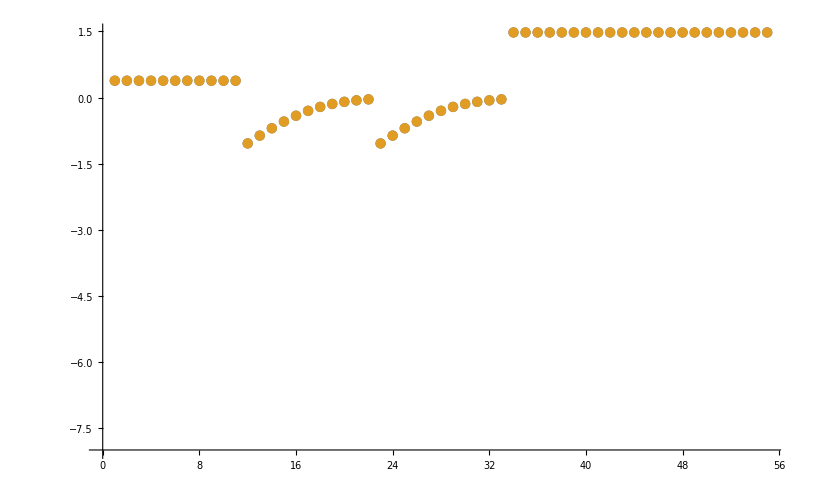

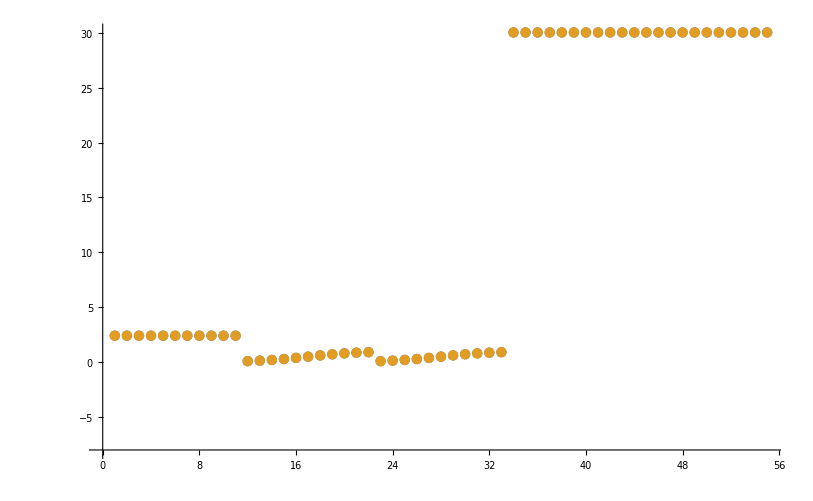

```mathematica
dataSetI=6;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

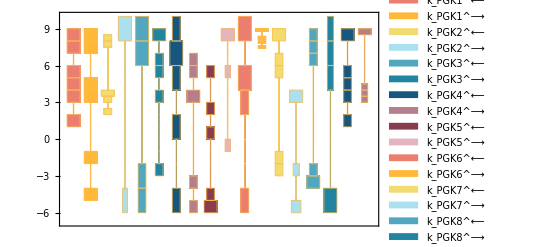

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[1;;6,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

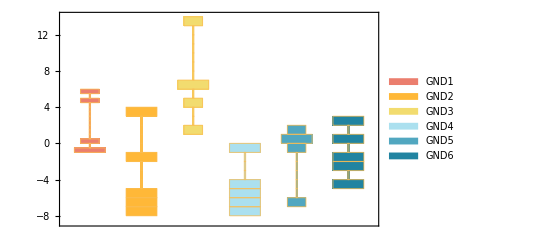

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

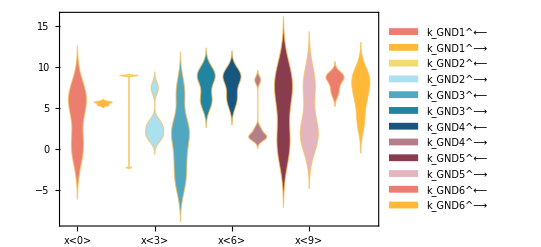

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

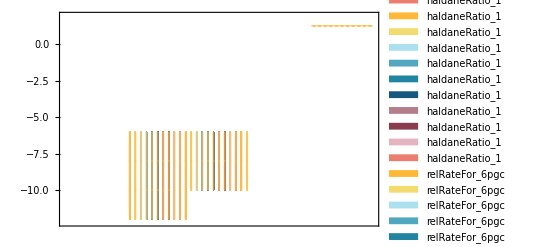

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataList[[1;;6,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

8.99748 | 8.33165 | 3.65551 | 8.41034 | 9. | 6.17915 | 8.24867 | 5.54191 | -4.23708 | 5.0768 | 5.06688 | 8.96013 | 6.29732 | 3.81841 | -2.1041 | -4.69709 | 4.0749 | 4.00532

#### Parameter Cluster Plots (Optional)

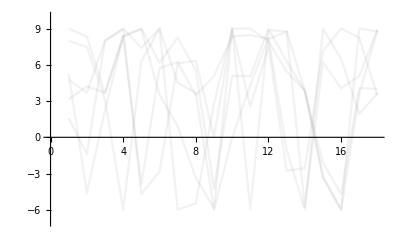

{-Graphics-}

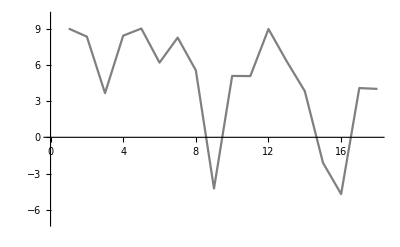

```mathematica
ListPlot[Log10[filteredDataList[[1;;6,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.000085 | 0.0000849964 | 0.00423497
0.000011 | 0.000011 | 0.000382447
0.0035 | 0.00349397 | 0.172288
0.0025 | 0.00249693 | 0.122993

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
2327.18 | 2327.18 | 0.0000555702

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
1900 | 1900. | 3.69725×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
1900 | 1900. | 3.69725×10^-6

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

Set::shape: Lists {predictedParameters,predictedParameterErrors} and exportPredictedParametersAndErrors[((6pgc)^c+nadp^c⇌co2^c+nadph^c+ru5p__D^c)^GND,GND,«20»,{Priority,6pgc[c],co2[c],nadp[c],nadph[c],ru5p__D[c],param_GND_total,param_pH,param_Temp,FileFlag,Target_Data}] are not the same shape.

Part::take: Cannot take positions 3 through -1 in predictedParameterErrors.

Part::partd: Part specification predictedParameterErrors⟦1⟧ is longer than depth of object.

BoxWhiskerChart::ldata: Transpose[predictedParameterErrors⟦3;;All⟧] is not a valid dataset or list of datasets.

BoxWhiskerChart[Transpose[predictedParameterErrors⟦3;;All⟧],ChartLabels→{predictedParameterErrors⟦1⟧}]

## Export data

```mathematica
directoryExport = "C:\\Users\\Daniel Zielinski\\Desktop\\MASSpy Work\\"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 7;
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pps

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pps\rateconst_labels_pps.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pps\S_pps.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_PPS[c],E_PPS[c]&pep,E_PPS[c]&pyr,E_PPS[c]&pep&amp,E_PPS[c]&pyr&atp,amp[c],atp[c],pep[c],pi[c],pyr[c],E_PPS[c]&pep&amp&pi}

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pps\species_pps.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{PPS1: E_PPS[c] + pyr[c] <=> E_PPS[c]&pyr,PPS2: E_PPS[c]&pep <=> E_PPS[c] + pep[c],PPS3: atp[c] + E_PPS[c]&pyr <=> E_PPS[c]&pyr&atp,PPS4: E_PPS[c]&pep&amp <=> amp[c] + E_PPS[c]&pep,PPS5: E_PPS[c]&pyr&atp <=> E_PPS[c]&pep&amp&pi,PPS6: E_PPS[c]&pep&amp&pi <=> E_PPS[c]&pep&amp + pi[c]}

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pps\reactions_pps.txt

```mathematica
solEnz = Import["C:/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_PPS[c],E_PPS[c]&pep,E_PPS[c]&pyr,E_PPS[c]&pep&amp,E_PPS[c]&pyr&atp,E_PPS[c]&pep&amp&pi}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_PPS1_rev*k_PPS2_fwd*k_PPS3_rev*k_PPS4_fwd*k_PPS5_rev*param_PPS_total) - k_PPS1_rev*k_PPS2_fwd*k_PPS3_rev*k_PPS4_fwd*k_PPS6_fwd*param_PPS_total - k_PPS1_rev*k_PPS2_fwd*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd*param_PPS_total - atp(c)*k_PPS2_fwd*k_PPS3_fwd*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd*param_PPS_total - k_PPS1_rev*k_PPS2_fwd*k_PPS3_rev*k_PPS5_rev*k_PPS6_rev*param_PPS_total*pi(c) - amp(c)*k_PPS1_rev*k_PPS3_rev*k_PPS4_rev*k_PPS5_rev*k_PPS6_rev*param_PPS_total*pi(c))/(k_PPS1_rev*k_PPS2_fwd*k_PPS3_rev*k_PPS4_fwd*k_PPS5_rev + k_PPS1_rev*k_PPS2_fwd*k_PPS3_rev*k_PPS4_fwd*k_PPS6_fwd + k_PPS1_rev*k_PPS2_fwd*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd + atp(c)*k_PPS2_fwd*k_PPS3_fwd*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd + k_PPS1_rev*k_PPS2_rev*k_PPS3_rev*k_PPS4_fwd*k_PPS5_rev*pep(c) + amp(c)*k_PPS1_rev*k_PPS2_rev*k_PPS3_rev*k_PPS4_rev*k_PPS5_rev*pep(c) + k_PPS1_rev*k_PPS2_rev*k_PPS3_rev*k_PPS4_fwd*k_PPS6_fwd*pep(c) + amp(c)*k_PPS1_rev*k_PPS2_rev*k_PPS3_rev*k_PPS4_rev*k_PPS6_fwd*pep(c) + k_PPS1_rev*k_PPS2_rev*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd*pep(c) + atp(c)*k_PPS2_rev*k_PPS3_fwd*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd*pep(c) + amp(c)*k_PPS1_rev*k_PPS2_rev*k_PPS4_rev*k_PPS5_fwd*k_PPS6_fwd*pep(c) + amp(c)*atp(c)*k_PPS2_rev*k_PPS3_fwd*k_PPS4_rev*k_PPS5_fwd*k_PPS6_fwd*pep(c) + k_PPS1_rev*k_PPS2_fwd*k_PPS3_rev*k_PPS5_rev*k_PPS6_rev*pi(c) + amp(c)*k_PPS1_rev*k_PPS3_rev*k_PPS4_rev*k_PPS5_rev*k_PPS6_rev*pi(c) + amp(c)*k_PPS1_rev*k_PPS2_rev*k_PPS3_rev*k_PPS4_rev*k_PPS6_rev*pep(c)*pi(c) + amp(c)*k_PPS1_rev*k_PPS2_rev*k_PPS4_rev*k_PPS5_fwd*k_PPS6_rev*pep(c)*pi(c) + amp(c)*atp(c)*k_PPS2_rev*k_PPS3_fwd*k_PPS4_rev*k_PPS5_fwd*k_PPS6_rev*pep(c)*pi(c) + k_PPS1_rev*k_PPS2_rev*k_PPS3_rev*k_PPS5_rev*k_PPS6_rev*pep(c)*pi(c) + amp(c)*k_PPS1_rev*k_PPS2_rev*k_PPS4_rev*k_PPS5_rev*k_PPS6_rev*pep(c)*pi(c) + amp(c)*atp(c)*k_PPS2_rev*k_PPS3_fwd*k_PPS4_rev*k_PPS5_rev*k_PPS6_rev*pep(c)*pi(c) + amp(c)*k_PPS2_rev*k_PPS3_rev*k_PPS4_rev*k_PPS5_rev*k_PPS6_rev*pep(c)*pi(c) + atp(c)*k_PPS1_fwd*k_PPS2_fwd*k_PPS3_fwd*k_PPS4_fwd*k_PPS5_fwd*pyr(c) + atp(c)*k_PPS1_fwd*k_PPS2_fwd*k_PPS3_fwd*k_PPS4_fwd*k_PPS5_rev*pyr(c) + k_PPS1_fwd*k_PPS2_fwd*k_PPS3_rev*k_PPS4_fwd*k_PPS5_rev*pyr(c) + atp(c)*k_PPS1_fwd*k_PPS2_fwd*k_PPS3_fwd*k_PPS4_fwd*k_PPS6_fwd*pyr(c) + k_PPS1_fwd*k_PPS2_fwd*k_PPS3_rev*k_PPS4_fwd*k_PPS6_fwd*pyr(c) + atp(c)*k_PPS1_fwd*k_PPS2_fwd*k_PPS3_fwd*k_PPS5_fwd*k_PPS6_fwd*pyr(c) + k_PPS1_fwd*k_PPS2_fwd*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd*pyr(c) + atp(c)*k_PPS1_fwd*k_PPS3_fwd*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd*pyr(c) + amp(c)*atp(c)*k_PPS1_fwd*k_PPS3_fwd*k_PPS4_rev*k_PPS5_fwd*k_PPS6_fwd*pyr(c) + atp(c)*k_PPS1_fwd*k_PPS2_fwd*k_PPS3_fwd*k_PPS5_fwd*k_PPS6_rev*pi(c)*pyr(c) + amp(c)*atp(c)*k_PPS1_fwd*k_PPS3_fwd*k_PPS4_rev*k_PPS5_fwd*k_PPS6_rev*pi(c)*pyr(c) + atp(c)*k_PPS1_fwd*k_PPS2_fwd*k_PPS3_fwd*k_PPS5_rev*k_PPS6_rev*pi(c)*pyr(c) + k_PPS1_fwd*k_PPS2_fwd*k_PPS3_rev*k_PPS5_rev*k_PPS6_rev*pi(c)*pyr(c) + amp(c)*atp(c)*k_PPS1_fwd*k_PPS3_fwd*k_PPS4_rev*k_PPS5_rev*k_PPS6_rev*pi(c)*pyr(c) + amp(c)*k_PPS1_fwd*k_PPS3_rev*k_PPS4_rev*k_PPS5_rev*k_PPS6_rev*pi(c)*pyr(c)))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pps\rateconst_clusters_pps.txt

```mathematica
solRateEq = Import["C:/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pps\rateLaw_pps.txt